```mathematica
data=Import["/home/s3377910/HiggsScan/compare_fs2/pole_masses_xt"];
```

```mathematica
cleanData=Cases[data,Except[{__,0}]];
```

```mathematica
{ms,ma2,tanBeta,at}=DeleteDuplicates/@Table[cleanData[[All,k]],{k,1,4}];
```

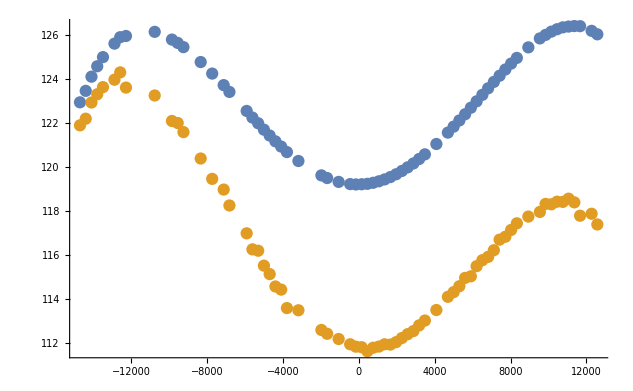

```mathematica
ListPlot[{Cases[cleanData,{ms[[1]],ma2[[1]],tanBeta[[1]],xt_,mhEFT_,_}:>{xt,mhEFT}],Cases[cleanData,{ms[[1]],ma2[[1]],tanBeta[[1]],xt_,_,mhFS_}:>{xt,mhFS}]}]
```

```mathematica
Sqrt[ma2[[1]]]
```

200.